```mathematica
Fsp[q_,R_]:=4/3*Pi*R^3*(Sin[q*R]-q*R*Cos[q*R])/(q*R)^3
```

```mathematica
LogNorm[r_,mu_,sigma_]:=(√(2 π) sigma)^(-1)/r*Exp[-Log[r/mu]^2/(2*sigma^2)]
```

```mathematica
Integrate[LogNorm[r,mu,sigma],{r,0,Infinity},Assumptions->sigma>0 && mu>0]
```

1

```mathematica
Integrate[Fsp[q,R]^2*BesselJ[0,q*r]*q,{q,0,Infinity},Assumptions->q>=0&&r>=0&&R>0&&r<2*R]
```

Integrate[(16 π^2 BesselJ[0,q r] (-q R Cos[q R]+Sin[q R])^2)/(9 q^5),{q,0,∞},Assumptions→q≥0&&r≥0&&R>0&&r<2 R]

```mathematica
Irsph[r_,R_,eta_]:=Module[{xi=r/(2*R)},Piecewise[{{eta^2 π R^4 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))]),r<=2*R}},0]]
```

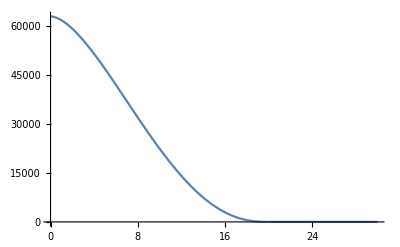

```mathematica
Plot[Irsph[r,10,1],{r,0,30},PlotRange->All]
```

```mathematica
GammaSD[x_,theta_,k_]:=1/theta*(x/theta)^(k-1)*Exp[-x/theta]/Gamma[k]
```

```mathematica
Integrate[Irsph[r,R,eta]*GammaSD[R,theta,k],{R,0,Infinity}]
```

$Aborted

```mathematica
Integrate[Irsph[r,R,eta]*LogNorm[R,mu,sigma],{R,0,Infinity}]
```

$Aborted

```mathematica
FullSimplify[Integrate[Fsp[q,R,eta,4/3*Pi*R^3]^2*q*lambda^2/(2*Pi),{q,0,qu}]]
```

(eta^2 lambda^2 π (-1-2 qu^2 R^2+2 qu^4 R^4+Cos[2 qu R]+2 qu R Sin[2 qu R]))/qu^4

```mathematica
FullSimplify[Integrate[Fsp[q,R,eta,Vp]^2*q*lambda^2/(2*Pi),{q,0,qu}]]
```

(9 eta^2 lambda^2 Vp^2 (-1-2 qu^2 R^2+2 qu^4 R^4+Cos[2 qu R]+2 qu R Sin[2 qu R]))/(16 π qu^4 R^6)

```mathematica
Limit[(eta^2 lambda^2 π (-1-2 qu^2 R^2+2 qu^4 R^4+Cos[2 qu R]+2 qu R Sin[2 qu R]))/qu^4,qu->Infinity,Assumptions->R>0&&eta>0&&Vp>0]
```

2 eta^2 lambda^2 π R^4

```mathematica
Limit[(9 eta^2 lambda^2 Vp^2 (-1-2 qu^2 R^2+2 qu^4 R^4+Cos[2 qu R]+2 qu R Sin[2 qu R]))/(16 π qu^4 R^6),qu->Infinity,Assumptions->R>0&&eta>0&&Vp>0]
```

(9 eta^2 lambda^2 Vp^2)/(8 π R^2)

```mathematica
FullSimplify[Integrate[Fsp[q,R,eta,4/3*Pi*R^3]^2*q,{q,0,Infinity}]/(4*Pi),Assumptions->R>0]
```

eta^2 π R^4

```mathematica
ComplexExpand[Exp[I*a]]
```

Cos[a]+ⅈ Sin[a]

```mathematica
Integrate[BesselJ[0,q*r*zeta]*zeta*(1-Exp[I*nu*Sqrt[1-zeta^2]]),{zeta,0,1}]
```

∫_0^1 (1-ⅇ^(ⅈ nu √(1-zeta^2))) zeta BesselJ[0,q r zeta]ⅆzeta